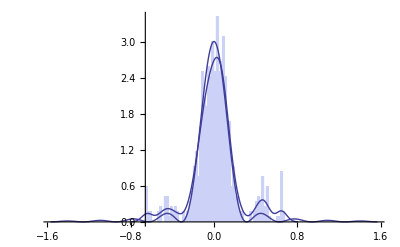

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingle.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],SmoothHistogram[ReadDataSingle,0.05,PlotStyle->Thick],Plot[3.0Sinc[10x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

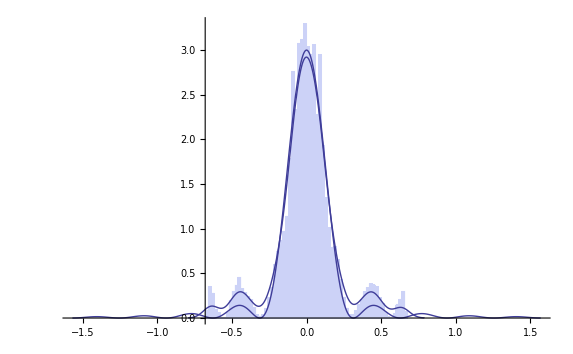

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleTest.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],SmoothHistogram[ReadDataSingle,0.05,PlotStyle->Thick],Plot[3.0Sinc[10x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

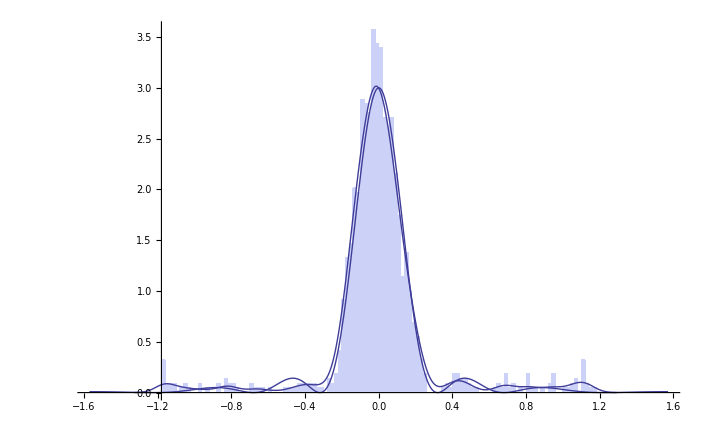

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleTest3.dat"]];

Show[{Histogram[ReadDataSingle,100,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,True}],SmoothHistogram[ReadDataSingle,0.05,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

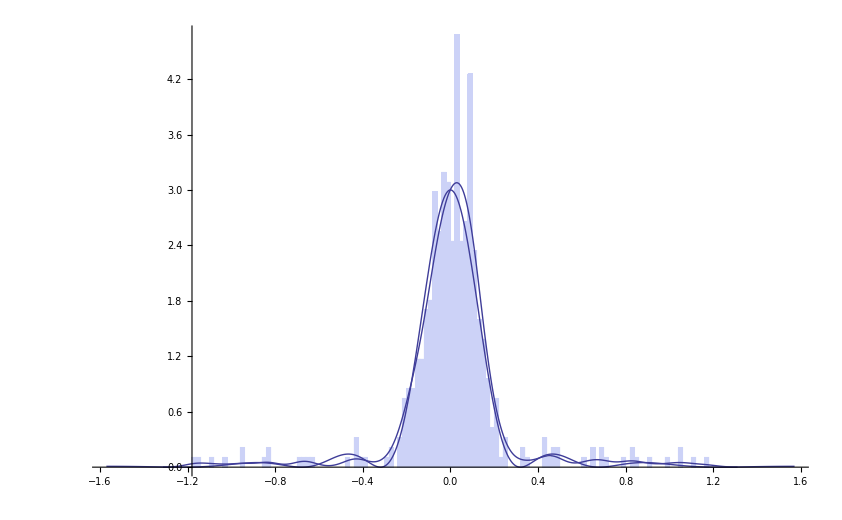

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleTest4.dat"]];

Show[{Histogram[ReadDataSingle,100,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,True}],SmoothHistogram[ReadDataSingle,0.05,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

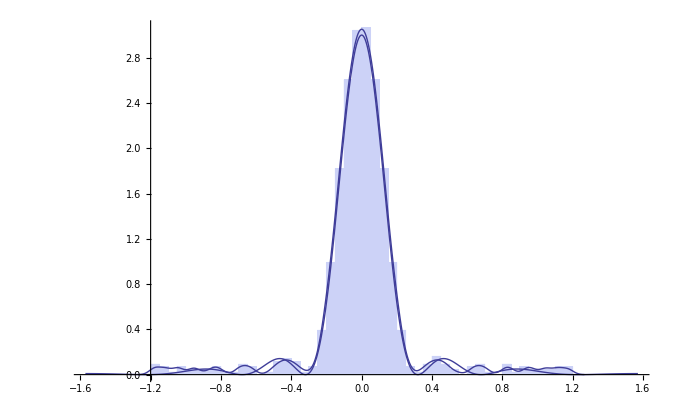

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleTest5.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,True}],SmoothHistogram[ReadDataSingle,0.03,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

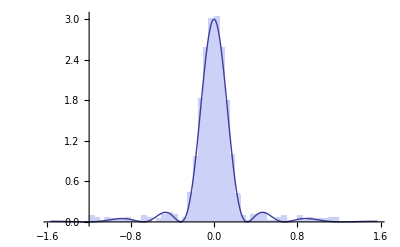

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleTest6.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

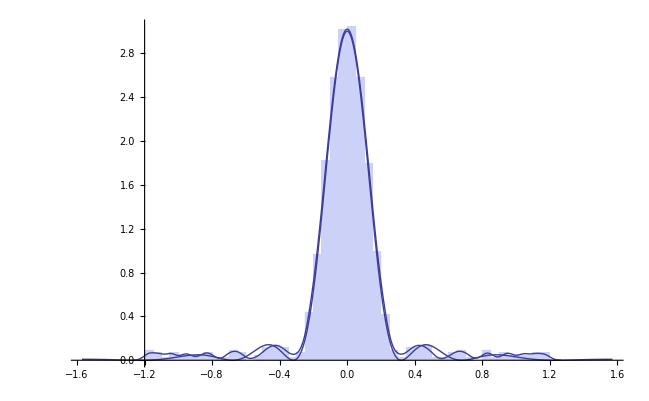

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianSingleTest6.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],SmoothHistogram[ReadDataSingle,0.03,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

```mathematica
VelocityField3[x_, t_, d_ ]:=-(√(2/π) Sin[(d x)/(2 t)] (Cos[(d^2+x^2)/(4 t)] (FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)]) Sin[(d^2+x^2)/(4 t)]))/(√t ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2))
```

```mathematica
NDSolve[{D[y[t], t]==-VelocityField3[y[t], t, 5 ]2,y[0.01]== RandomVariate[UniformDistribution[{-5,5}]]},y,{t,1,100}]
```

{{y→InterpolatingFunction[{{1.,100.}},<>]}}

```mathematica
MyHank[x_,t_, d_] = ((FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2)
```

(FresnelC[(d-x)/(√(2 π) √t)]+FresnelC[(d+x)/(√(2 π) √t)])^2+(FresnelS[(d-x)/(√(2 π) √t)]+FresnelS[(d+x)/(√(2 π) √t)])^2

```mathematica
BohmianForce[x_] = -D[D[MyHank[x,20, 10],x,x]/MyHank[x,20, 10],x]
```

((2 (-Cos[1/80 (10-x)^2]/(2 √(10 π))+Cos[1/80 (10+x)^2]/(2 √(10 π))) (FresnelC[(10-x)/(2 √(10 π))]+FresnelC[(10+x)/(2 √(10 π))])+2 (FresnelS[(10-x)/(2 √(10 π))]+FresnelS[(10+x)/(2 √(10 π))]) (-Sin[1/80 (10-x)^2]/(2 √(10 π))+Sin[1/80 (10+x)^2]/(2 √(10 π)))) (2 (-Cos[1/80 (10-x)^2]/(2 √(10 π))+Cos[1/80 (10+x)^2]/(2 √(10 π)))^2+2 (-((-10+x) Cos[1/80 (10-x)^2])/(80 √(10 π))+((10+x) Cos[1/80 (10+x)^2])/(80 √(10 π))) (FresnelS[(10-x)/(2 √(10 π))]+FresnelS[(10+x)/(2 √(10 π))])+2 (-Sin[1/80 (10-x)^2]/(2 √(10 π))+Sin[1/80 (10+x)^2]/(2 √(10 π)))^2+2 (FresnelC[(10-x)/(2 √(10 π))]+FresnelC[(10+x)/(2 √(10 π))]) (((-10+x) Sin[1/80 (10-x)^2])/(80 √(10 π))-((10+x) Sin[1/80 (10+x)^2])/(80 √(10 π)))))/((FresnelC[(10-x)/(2 √(10 π))]+FresnelC[(10+x)/(2 √(10 π))])^2+(FresnelS[(10-x)/(2 √(10 π))]+FresnelS[(10+x)/(2 √(10 π))])^2)^2-(2 (FresnelC[(10-x)/(2 √(10 π))]+FresnelC[(10+x)/(2 √(10 π))]) (((-10+x)^2 Cos[1/80 (10-x)^2])/(3200 √(10 π))-((10+x)^2 Cos[1/80 (10+x)^2])/(3200 √(10 π))+Sin[1/80 (10-x)^2]/(80 √(10 π))-Sin[1/80 (10+x)^2]/(80 √(10 π)))+6 (-((-10+x) Cos[1/80 (10-x)^2])/(80 √(10 π))+((10+x) Cos[1/80 (10+x)^2])/(80 √(10 π))) (-Sin[1/80 (10-x)^2]/(2 √(10 π))+Sin[1/80 (10+x)^2]/(2 √(10 π)))+6 (-Cos[1/80 (10-x)^2]/(2 √(10 π))+Cos[1/80 (10+x)^2]/(2 √(10 π))) (((-10+x) Sin[1/80 (10-x)^2])/(80 √(10 π))-((10+x) Sin[1/80 (10+x)^2])/(80 √(10 π)))+2 (FresnelS[(10-x)/(2 √(10 π))]+FresnelS[(10+x)/(2 √(10 π))]) (-Cos[1/80 (10-x)^2]/(80 √(10 π))+Cos[1/80 (10+x)^2]/(80 √(10 π))+((-10+x)^2 Sin[1/80 (10-x)^2])/(3200 √(10 π))-((10+x)^2 Sin[1/80 (10+x)^2])/(3200 √(10 π))))/((FresnelC[(10-x)/(2 √(10 π))]+FresnelC[(10+x)/(2 √(10 π))])^2+(FresnelS[(10-x)/(2 √(10 π))]+FresnelS[(10+x)/(2 √(10 π))])^2)

```mathematica
HydroForce[x_] = -D[MyHank[x,20, 10],x]
```

-2 (-Cos[1/80 (10-x)^2]/(2 √(10 π))+Cos[1/80 (10+x)^2]/(2 √(10 π))) (FresnelC[(10-x)/(2 √(10 π))]+FresnelC[(10+x)/(2 √(10 π))])-2 (FresnelS[(10-x)/(2 √(10 π))]+FresnelS[(10+x)/(2 √(10 π))]) (-Sin[1/80 (10-x)^2]/(2 √(10 π))+Sin[1/80 (10+x)^2]/(2 √(10 π)))

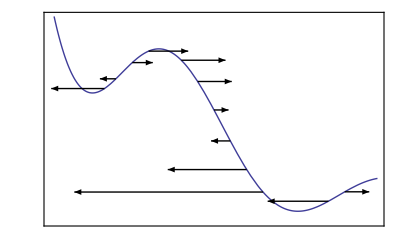

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[Abs[N[BohmianForce[x]/Max[Table[BohmianForce[x],{x,{13.3,14,16,18,19,20,21,22,27,28}}]]]/25]],Arrow[{{x,MyHank[x,20, 10]},{x+40BohmianForce[x],MyHank[x,20, 10]}}]}],{x,{13.3,14,15,16,18,19,20,21,22,23,27,28}}];
Show[Plot[{MyHank[x,20, 10]},{x,10,30},PlotRange->{Full,{0,0.3}},Frame->True,Axes->True,FrameTicks->None],MyForceTestArrows]
```

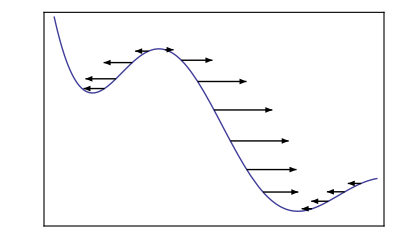

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[Abs[N[HydroForce[x]/Max[Table[HydroForce[x],{x,{13.3,14,15,16,18,19,20,21,22,27,28}}]]/10]]],Arrow[{{x,MyHank[x,20, 10]},{x+80HydroForce[x],MyHank[x,20, 10]}}]}],{x,{13.3,14,15,16,17,18,19,20,21,22,23,26,27,28,29}}];
Show[Plot[{MyHank[x,20, 10]},{x,10,30},PlotRange->{Full,{0,0.3}},Frame->True,Axes->True,FrameTicks->None],MyForceTestArrows]
```

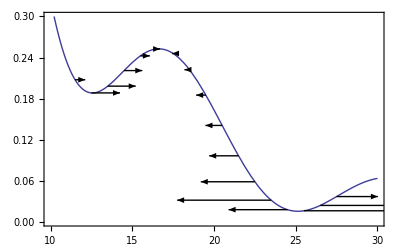

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[0.03],Arrow[{{x,MyHank[x,20, 10]},{x+20BohmianForce[x],MyHank[x,20, 10]}}]}],{x,11.5,28}];
Show[Plot[{MyHank[x,20, 10]},{x,10,30},PlotRange->{Full,{0,0.3}},Frame->True,Axes->True,FrameTicks->{True,True}],MyForceTestArrows]
```

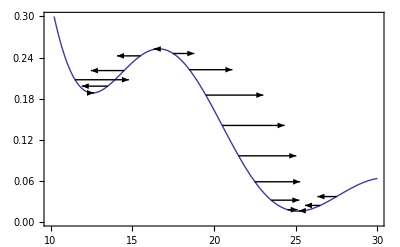

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[0.03],Arrow[{{x,MyHank[x,20, 10]},{x+84HydroForce[x],MyHank[x,20, 10]}}]}],{x,11.5,28}];
Show[Plot[{MyHank[x,20, 10]},{x,10,30},PlotRange->{Full,{0,0.3}},Frame->True,Axes->True,FrameTicks->{True,True}],MyForceTestArrows]
```

```mathematica
yyyHank[x_,y_,t_,k_,w_]:=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t]+BesselJ[0,k √(x^2+(y+d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y+d)^2)] Sin[w t])/(18),{d,3,7,0.5}]
yyyHankSingle[x_,y_,t_,k_,w_]:=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t])/(25),{d,-6,6,0.5}]
```

```mathematica
DaForceX[x_,y_,t_,k_,w_] = -D[-yyyHank[x,y,t,k,w],x];
DaForceY[x_,y_,t_,k_,w_] = -D[-yyyHank[x,y,t,k,w],y];
DaForceSingleX[x_,y_,t_,k_,w_] = -D[-yyyHankSingle[x,y,t,k,w],x];
DaForceSingleY[x_,y_,t_,k_,w_] = -D[-yyyHankSingle[x,y,t,k,w],y];
CosDisSqWidth[d_] = ProbabilityDistribution[Cos[x π/(2d)]^2/2,{x,-d,d}]
GaussianTanDisSqWidth[d_,σ_] = ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]
```

ProbabilityDistribution[1/2 Cos[(x π)/(2 d)]^2,{x,-d,d}]

ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]

```mathematica
yyyHankSingle[x,y,t,k,w]
```

1/18 (BesselJ[0,k √(x^2+(-6.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-6.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-5.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-5.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-5.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-5.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-4.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-4.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-4.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-4.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-3.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-3.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-3.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-3.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-2.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-2.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-2.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-2.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-1.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-1.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-1.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-1.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(-0.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(-0.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(0.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(0.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(0.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(0.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(1.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(1.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(1.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(1.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(2.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(2.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(2.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(2.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(3.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(3.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(3.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(3.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(4.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(4.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(4.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(4.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(5.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(5.+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(5.5+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(5.5+y)^2)] Sin[t w])+1/18 (BesselJ[0,k √(x^2+(6.+y)^2)] Cos[t w]+BesselY[0,k √(x^2+(6.+y)^2)] Sin[t w])

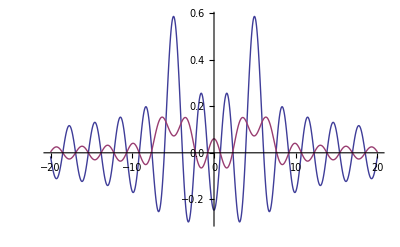

```mathematica
Plot[{(BesselJ[0,2 (y+5)]+BesselJ[0,2 (y-5)])/2,yyyHank[0,y,0,2,2]},{y,-20,20},PlotRange->All]
```

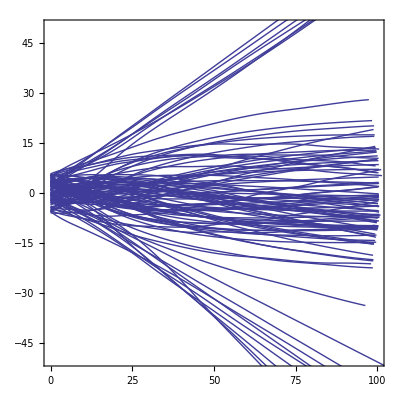

```mathematica
AAA =  1.0;
ddd = 6.0;
www = 1;
x000 = 0.0;
v000 = 1.0;
kkk= 1;
disss = 0.0;
tmax = 100;
NMAX=100;
swidth = 2;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceSingleX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceSingleY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== RandomVariate[UniformDistribution[{-ddd,ddd}]],y'[0]== v000 Sin[RandomVariate[GaussianTanDisSqWidth[π/2,1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU},{t,0,tmax},PlotRange->{{0,tmax},{-tmax/2,tmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

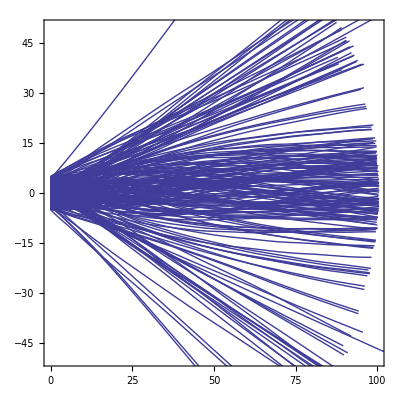

```mathematica
AAA =  1.0;
ddd = 5.0;
www = 1;
x000 = 0.0;
v000 = 1.0;
kkk= 1;
disss = 0.0;
tmax = 100;
NMAX=200;
swidth = 2;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceSingleX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceSingleY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== RandomVariate[UniformDistribution[{-ddd,ddd}]],y'[0]== v000 Sin[RandomVariate[GaussianTanDisSqWidth[π/2,1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU},{t,0,tmax},PlotRange->{{0,tmax},{-tmax/2,tmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA = 2.0;
ddd = 5.0;
www = 2;
x000 = 0.0;
v000 = 1.0;
kkk= 2;
disss = 0.0;
tmax = 100;
CHUNK = 100;
REPEAT = 100;
CUTTOFF = 70;

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitA2.dat"];

Do[
Parallelize[Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceSingleX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceSingleY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== RandomVariate[UniformDistribution[{-ddd,ddd}]],y'[0]== v000 Sin[RandomVariate[GaussianTanDisSqWidth[π/2,1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{CHUNK}];
]

TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

Set::write: Tag Times in Null\ {« 1 »} is Protected.

$Aborted

/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitA2.dat

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Histogram::ldata: Flatten[$Failed] is not a valid dataset or list of datasets.

SmoothHistogram::ldata: Flatten[$Failed] is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in {Histogram[Flatten[$Failed], 50, .

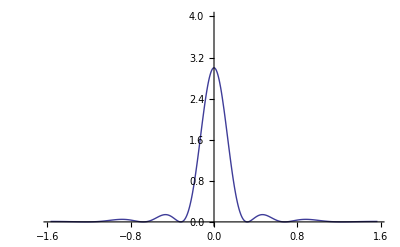
Show[{Histogram[Flatten[$Failed],50,PDF,PlotRange→{{-π/2,π/2},Full},Axes→{True,False}],SmoothHistogram[Flatten[$Failed],0.04,PlotStyle→Thickness[Large]],-Graphics-}]

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitA2.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],SmoothHistogram[ReadDataSingle,0.04,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitA2.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],SmoothHistogram[ReadDataSingle,0.04,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

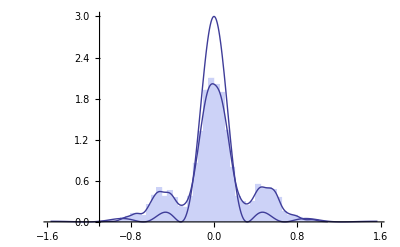

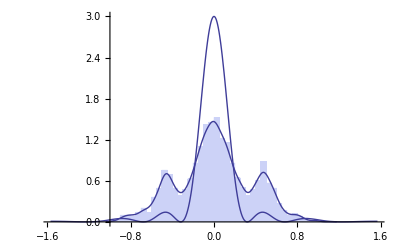

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitA05.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],SmoothHistogram[ReadDataSingle,0.04,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

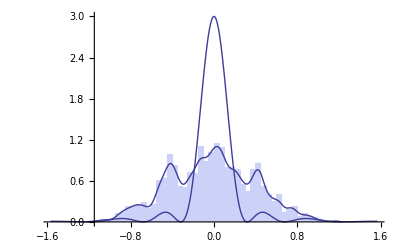

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitA02.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],SmoothHistogram[ReadDataSingle,0.04,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

```mathematica
AAA = 2.0;
ddd = 5.0;
www = 2;
x000 = 0.0;
v000 = 1.0;
kkk= 2;
disss = 0.0;
tmax = 100;
CHUNK = 10;
REPEAT = 100;
CUTTOFF = 90;
MEMORY=100;

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitA2M300.dat"];

Do[

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA DaForceSingleX[x[t],y[t],t,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA DaForceSingleY[x[t],y[t],t,kkk,www]-disss  D[y[t],t]),y[0]== RandomVariate[UniformDistribution[{-ddd,ddd}]],y'[0]== v000 Sin[RandomVariate[GaussianTanDisSqWidth[π/2,1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{CHUNK}];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

$Aborted

/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitA2M300.dat

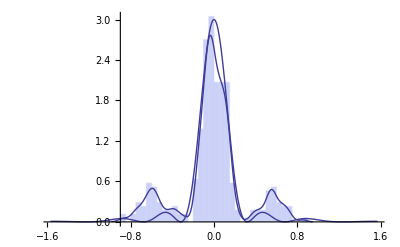

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitA2M300.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],SmoothHistogram[ReadDataSingle,0.04,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

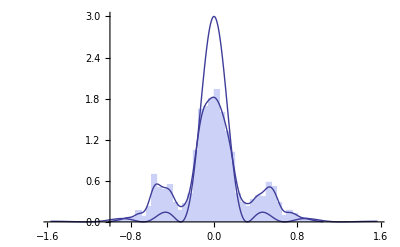

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroSingleSlitM300.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False}],SmoothHistogram[ReadDataSingle,0.04,PlotStyle->Thick],Plot[3.0Sinc[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

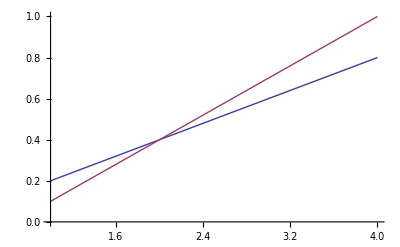

```mathematica
ListLinePlot[{{{1,0.2},{2,0.4},{3,0.6},{4,0.8}},{{1,0.1},{2,0.4},{3,0.7},{4,1.0}}},PlotRange->{Full,{0,1}}]
```

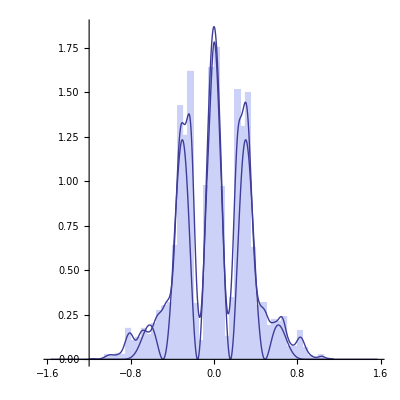

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlit.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],SmoothHistogram[ReadDataSingle,0.03,PlotStyle->Thick],Plot[1.5(ⅇ^(-Sec[x]^2/0.5^2))/(π Erfc[1/0.5])Cos[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

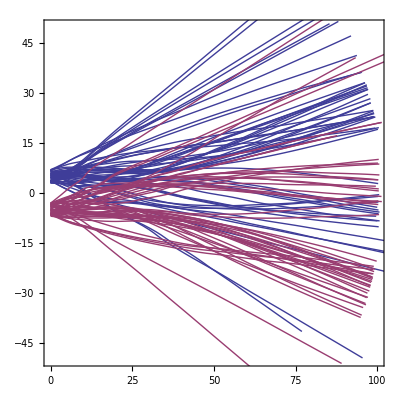

```mathematica
AAA =  1.0;
ddd = 5.0;
www = 2;
x000 = 0.0;
v000 = 1.0;
kkk= 2;
disss = 0.0;
tmax = 100;
NMAX=50;
swidth = 2;
MEMORY = 100;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA DaForceY[x[t],y[t],t,kkk,www]-disss  D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-2,2}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA  DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t]), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA  DaForceY[x[t],y[t],t,kkk,www]-disss D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-2,2}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,tmax},{-tmax/2,tmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA = 1.0;
ddd = 5.0;
www = 2;
x000 = 0.0;
v000 = 1.0;
kkk= 2;
disss = 0.0;
tmax = 100;
CHUNK = 10;
REPEAT = 100;
CUTTOFF = 90;
MEMORY = 1;

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitM01C90.dat"];

Do[


Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA DaForceX[x[t],y[t],t,kkk,www]-disss (D[x[t],t])), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA DaForceY[x[t],y[t],t,kkk,www]-disss(D[y[t],t])),y[0]== 5+RandomVariate[UniformDistribution[{-2,2}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA DaForceX[x[t],y[t],t,kkk,www]-disss (D[x[t],t])), D[y[t],t,t] ==ⅇ^(-t/MEMORY)( AAA  DaForceY[x[t],y[t],t,kkk,www]-disss (D[y[t],t])),y[0]== -5+RandomVariate[UniformDistribution[{-2,2}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{CHUNK}];



TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitM01C90.dat

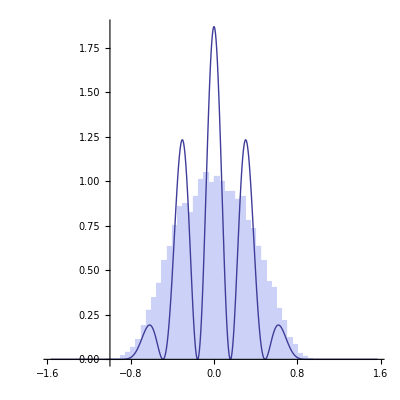

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitM01C90.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[1.5(ⅇ^(-Sec[x]^2/0.5^2))/(π Erfc[1/0.5])Cos[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

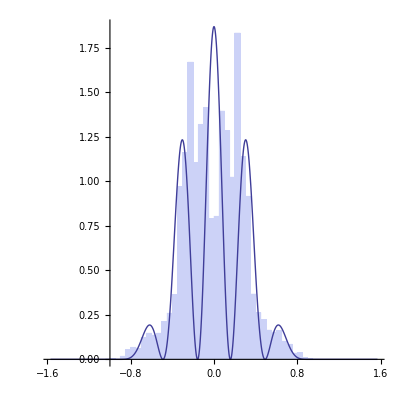

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitM50C90.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[1.5(ⅇ^(-Sec[x]^2/0.5^2))/(π Erfc[1/0.5])Cos[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

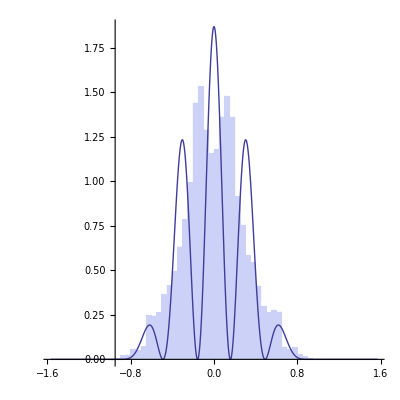

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitM10C90.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[1.5(ⅇ^(-Sec[x]^2/0.5^2))/(π Erfc[1/0.5])Cos[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

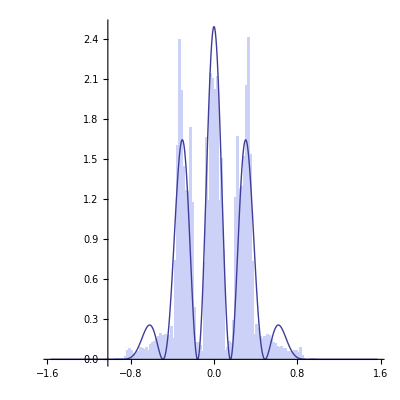

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitM300C90.dat"]];

Show[{Histogram[ReadDataSingle,100,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],Plot[2.0(ⅇ^(-Sec[x]^2/0.5^2))/(π Erfc[1/0.5])Cos[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```